```mathematica
logm={1,5.96,8.212,9.992,18.684,21.072,22.796,24.216,26.148,26.508,28.828,28.636,30.012,31.86,31.912,32.84,59.568,63.756,65.924,65.34,67.804,67.864,66.432,70.312,71.6,71.644,73.38,74.92,75.828,77.328,78.912,77.904,81.38,81.736,83.68,80.332,84.336,85.24,86.42,85.152,85.804,88.472,90.552,164.32,156.008,157.088,161.004,169.624,164.82,167.404,167.32,166.268,166.836,168.544,172.788,177.248,179.268,176.18,176.852,176.104,180.644,185.376,182.256,187.996,185.852,184.336,189.732,187.996,189.036,187.524,189.024,190.704,192.9,195.332,194.532,196.824,195.92,193.976,199.468,197.796,197.284,202.716,202.708,204.188,206.348,202.64,209.588,206.688,209.024,207.98,209.012,207.104,210.228,207.48,216.616,215.132,212.512,214.992,222.66};
logstd={0,3.566286584109583,4.066332008087878,4.511312004284341,9.073044913368388,9.465453819019984,9.474301240724827,8.326904827125144,9.952592426096832,9.98328282680602,10.830993306248509,9.29212053301075,9.016199642865057,9.91243663283655,8.732940856320969,8.605951429098354,18.083732358116784,19.465057513400776,22.185901469176322,18.8855606218084,19.722413239763537,18.098549776156098,19.16406470454533,19.987962777631942,19.410100463418523,18.56009870663408,19.968665453655134,19.67987804840264,17.394206391784593,19.210112336995845,18.543361507558437,19.613433763622318,20.370851724952495,18.68716950209421,20.90726189628857,19.846354224390936,18.980598093843092,18.460509202077823,20.435155981787855,17.967996438111847,16.611489517800624,19.187944548596132,19.085473428762516,45.39940087710409,39.905387305475436,38.810208141673236,40.555788538752395,47.06568414460794,40.99516556863748,42.51983988681049,39.36721478591037,38.56802012030174,40.385456590213266,36.47103047625608,40.6574846246051,41.797446046379434,40.99536773831892,38.76539178184583,39.42950793504783,34.62411275397537,41.81728427337194,43.26405695262524,42.575373914975785,41.806075922047505,49.28795081964759,36.16494302497931,41.65818258157694,42.29198486711164,40.92161658585839,39.04173951042653,36.40339852266544,40.43949040232827,41.811505593556426,40.07649904869436,38.68520357966338,40.59587447019709,42.43886897644658,39.09843250054918,43.584503851713166,40.6601817998887,40.40677349158183,37.95296225592938,36.39305889864165,39.67952439231095,45.211711933966846,37.71300041099886,43.74784858710197,39.876793451831105,38.8926654267871,38.10453516315348,42.32176574766228,39.210064830346816,38.898946206806166,38.190700438719375,39.7520885489052,37.972655635338434,36.99278113362119,35.64525124052291,39.56867953318635};
logrec={1,2,9,16,11,18,25,32,51,70,89,108,145,182,219,256,83,102,121,140,159,178,197,216,253,290,327,364,401,438,475,512,573,634,695,756,817,878,939,1000,1091,1182,1273,356,375,394,413,432,469,506,543,580,617,654,691,728,765,802,839,876,913,950,987,1024,1085,1146,1207,1268,1329,1390,1451,1512,1573,1634,1695,1756,1817,1878,1939,2000,2091,2182,2273,2364,2455,2546,2637,2728,2819,2910,3001,3092,3183,3274,3365,3456,3583,3710,3837,3964,4091,4218,4345,4472,4599,4726,4853,4980,1345,1382,1419,1456,1493,1530,1567,1604,1641,1678,1715,1752,1789,1826,1863,1900,1937,1974,2011,2048,2109,2170,2231,2292,2353,2414,2475,2536,2597,2658,2719,2780,2841,2902,2963,3024,3085,3146,3207,3268,3329,3390,3451,3512,3573,3634,3695,3756,3817,3878,3939,4000,4091,4182,4273,4364,4455,4546,4637,4728,4819,4910,5001,5092,5183,5274,5365,5456,5547,5638,5729,5820,5911,6002,6093,6184,6275,6366,6457,6548,6639,6730,6821,6912,7039,7166,7293,7420,7547,7674,7801,7928,8055,8182,8309,8436,8563,8690,8817,8944,9071,9198,9325,9452,9579,9706,9833,9960,10087,10214,10341,10468,10595,10722,10849,10976,11145,11314,11483,11652,11821,11990,12159,12328,12497,12666,12835,13004,13173,13342,13511,13680,13849,14018,14187,14356,14525,14694,14863,15032,15201,15370,15539,15708,15877,16046,16215};
logreccont={2,9,16,17,24,43,62,81,70,89,108,145,182,219,256,209,246,283,320,381,442,347,384,445,506,567,628,689,570,631,692,753,814,875,966,817,878,939,1000,1091,1182,1273,1064,1125,1216,1307,1398,1489,1580,1671,1432,1523,1614,1705,1796,1887,1978,1739,1830,1921,2012,2103,2194,2285,2376,2137,2228,2319,2410,2501,2592,2719,2846,2535,2626,2717,2808,2935,3062,3189,3316,2933,3024,3151,3278,3405,3532,3659,3786,3913,3494,3621,3748,3875,4002,4129,4256,4383,3964,4091,4218,4345,4472,4599,4726,4853,4980,4561,4688,4815,4942,5069,5196,5323,5450,5031,5158,5285,5412,5539,5666,5793,5920,6047,5628,5755,5882,6009,6136,6263,6390,6517,6686,6225,6352,6479,6606,6733,6860,7029,7198,7367,6822,6949,7076,7203,7372,7541,7710,7879,8048,7419,7546,7715,7884,8053,8222,8391,8560,8729,8058,8227,8396,8565,8734,8903,9072,9241,9410,8739,8908,9077,9246,9415,9584,9753,9922,10091,9420,9589,9758,9927,10096,10265,10434,10603,10772,10941,10270,10439,10608,10777,10946,11115,11284,11453,11622,10951,11120,11289,11458,11627,11796,11965,12134,12303,11632,11801,11970,12139,12308,12477,12646,12815,12984,13153,12482,12651,12820,12989,13158,13327,13496,13665,13834,13163,13332,13501,13670,13839,14008,14177,14346,14515,14684,14013,14182,14351,14520,14689,14858,15027,15196,15365,15534,14863,15032,15201,15370,15539,15708,15877,16046,16215};
log2m={1,5.512,7.568,5.252,6.368,6.984,7.94,8.76,9.492,10.46,11.288,12.164,13.164,14.108,15.032,16.024,21.836,22.744,23.616,25.116,25.228,26.064,27.536,28.412,29.124,30.192,31.564,32.708,33.108,34.452,35.848,36.768,37.508,38.612,40.272,41.0,42.6,42.76,44.372,45.392,46.148,46.876,47.932,49.504,50.26,51.368,53.056,53.448,54.716,55.324,56.676,58.26,59.428,59.808,60.776,62.144,62.992,64.056,66.028,65.88,65.64,69.8,69.24,70.2,70.16,71.64,73.08,73.6,76.2,76.0,77.08,78.16,78.76,80.68,82.68,81.76,85.76,84.68,87.52,96.08,100.0,101.12,98.08,104.4,100.92,109.04,108.44,108.92,110.92,111.68,110.64,107.24,113.44,116.4,114.68,116.48,119.08,118.96,123.32};
log2std={0,3.1537051225502992,3.805965843251881,1.4270585131661562,1.518083001683373,1.1864838810535945,1.135077089893017,1.1859173664298874,0.8999644437420846,0.9509994742374993,0.6671251756604604,0.4744512619858862,0.42083726070774674,0.40041977973122156,0.21673947494630508,0.1530490117576719,3.7896047287283143,3.8717520581772793,3.849745965645006,4.151932562072751,3.236049443379999,3.677486097866313,4.004085913164202,3.6213610700950545,3.6238962457553887,3.813021898704491,3.9967366688337127,4.203657455121671,3.9497260664506846,3.944578050945373,4.488306584893683,4.545126620898476,3.913302441672506,4.356771281579973,4.603261452492135,4.067431622043571,4.767389222624895,4.308874563038474,4.385614666155703,4.762177653133071,4.588474256220688,4.402343012533213,4.779055973725355,4.6820918401928004,4.9242664428318665,4.2802541980588025,4.786320507446195,4.5360000000000005,4.968233488877107,4.826077496269615,4.63756660329531,5.353167286756505,5.242596303359624,5.063905212383028,4.851167282211571,5.115785765647346,5.17454693668924,5.0387363495225665,6.063267765817373,5.354026522160682,3.1984996482726085,5.223025942880239,5.573365231168688,6.362389488234746,4.105411063462464,4.533254901282301,5.059011761203961,5.973273809227232,5.215361924162119,4.898979485566356,4.058768286069062,4.066251344912166,5.255701665810189,6.354337101539389,5.842739083683268,5.046028141023394,6.694953323212942,4.985739664282522,5.657702713999738,6.638795071396616,8.059776671843954,11.638969026507459,9.9475424100629,9.006664199358163,9.686774488961742,11.119280552265959,11.607170197769998,10.688011976041196,8.366217783443126,10.189092206865144,9.24718335494652,7.9813783270811065,10.476946119933995,8.777243302996677,9.451856960407305,11.883164561681372,10.840368997409637,11.75578155632368,13.660805247129467};
log2rec={1,2,9,64,125,216,343,512,729,1000,1331,1728,2197,2744,3375,4096,1241,1458,1729,2000,2331,2662,3059,3456,3925,4394,4941,5488,6119,6750,7471,8192,9009,9826,10745,11664,12691,13718,14859,16000,17261,18522,19909,21296,22815,24334,25991,27648,29449,31250,33201,35152,37259,39366,41635,43904,46341,48778,51389,54000,56791,59582,62559,65536,68705,71874,75241,78608,82179,85750,89531,93312,97309,101306,105525,109744,114191,118638,123319,32000,33261,34522,35783,37044,38431,39818,41205,42592,44111,45630,47149,48668,50325,51982,53639,55296,57097,58898,60699,62500,64451,66402,68353,70304,72411,74518,76625,78732,81001,83270,85539,87808,90245,92682,95119,97556,100167,102778,105389,108000,110791,113582,116373,119164,122141,125118,128095,131072,134241,137410,140579,143748,147115,150482,153849,157216,160787,164358,167929,171500,175281,179062,182843,186624,190621,194618,198615,202612,206831,211050,215269,219488,223935,228382,232829,237276,241957,246638,251319,256000,260921,265842,270763,275684,280851,286018,291185,296352,301771,307190,312609,318028,323705,329382,335059,340736,346677,352618,358559,364500,370711,376922,383133,389344,395831,402318,408805,415292,422061,428830,435599,442368,449425,456482,463539,470596,477947,485298,492649,500000,507651,515302,522953,530604,538561,546518,554475,562432,570701,578970,587239,595508,604095,612682,621269,629856,638767,647678,656589,665500,674741,683982,693223,702464,712041,721618,731195,740772,750691,760610,770529,780448,790715,800982,811249,821516,832137,842758,853379,864000,874981,885962,896943,907924,919271,930618,941965,953312,965031,976750,988469,1000188,1012285,1024382,1036479};
ccm={1,3.,5.5,8.33333,11.4167,14.7,18.15,21.7429,25.4607,29.2897,33.2187,37.2385,41.3417,45.5219,49.7734,54.0917,58.4724,62.9119,67.4071,71.9548,76.5525,81.1979,85.8887,90.623,95.399,100.215,105.069,109.961,114.888,119.85,124.845,129.872,134.93,140.019,145.137,150.284,155.459,160.66,165.888,171.142,176.42,181.723,187.05,192.4,197.773,203.168,208.584,214.022,219.481,224.96,230.459,235.978,241.516,247.073,252.649,258.242,263.854,269.483,275.129,280.792,286.472,292.168,297.881,303.609,309.353,315.112,320.887,326.676,332.48,338.299,344.131,349.978,355.839,361.714,367.602,373.503,379.418,385.345,391.285,397.238,403.204,409.182,415.172,421.174,427.188,433.213,439.251,445.3,451.36,457.431,463.514,469.607,475.712,481.827,487.953,494.089,500.236,506.393,512.56,518.738};
ccstd={0,1.41876,2.60271,3.79736,4.9948,6.21852,7.44816,8.75069,9.96285,11.2531,12.5002,13.6977,15.0161,16.0786,17.4742,18.7756,20.0188,21.2791,22.3773,23.816,24.9141,26.0155,27.6513,28.6541,30.1381,31.3597,32.5489,33.9223,35.16,36.4004,37.9016,39.0827,40.2902,41.2617,42.9617,44.4204,45.5254,46.5008,47.9158,49.4052,50.6059,51.8307,53.2657,54.1988,55.3779,56.8065,58.1544,59.5276,60.6069,61.5547,63.1001,64.4323,66.0249,66.7696,68.2624,69.4107,70.7471,72.2395,73.663,75.1674,76.3233,77.5091,78.474,80.2666,81.0222,81.9956,83.4643,85.5005,86.05,87.6347,88.71,90.0957,91.337,92.3795,93.7054,95.4042,97.0415,98.0067,98.9922,100.766,101.522,102.997,104.742,105.69,107.924,108.057,109.135,109.872,111.633,112.568,114.092,115.223,116.67,118.82,119.184,120.99,121.966,123.063,123.652,125.846};
ccrec={1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255};
lsm={1,3.072,4.364,5.444,6.204,7.0,7.952,8.784,9.64,10.448,11.268,12.28,13.104,14.112,15.028,16.02,17.004,18.0,19.004,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99};
lsstd={0,1.3246946818040752,1.4448197119364063,1.3201757458762828,1.4458160325573928,1.4226735395022991,1.1268078806966164,1.1177405781307217,1.0307278981380101,0.86214615930247,0.5763471176296451,0.7166589146867567,0.4349528710101819,0.384,0.1876592656918384,0.20880613017821106,0.063118935352238,0.0,0.063118935352238,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
lsrec={1,8,27,64,125,216,343,512,729,1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000,9261,10648,12167,13824,15625,17576,19683,21952,24389,27000,29791,32768,35937,39304,42875,46656,50653,54872,59319,64000,68921,74088,79507,85184,91125,97336,103823,110592,117649,125000,132651,140608,148877,157464,166375,175616,185193,195112,205379,216000,226981,238328,250047,262144,274625,287496,300763,314432,328509,343000,357911,373248,389017,405224,421875,438976,456533,474552,493039,512000,531441,551368,571787,592704,614125,636056,658503,681472,704969,729000,753571,778688,804357,830584,857375,884736,912673,941192,970299,1000000,1030301,1061208,1092727,1124864,1157625,1191016,1225043,1259712,1295029,1331000,1367631,1404928,1442897,1481544,1520875,1560896,1601613,1643032,1685159,1728000,1771561,1815848,1860867,1906624,1953125,2000376,2048383,2097152,2146689,2197000,2248091,2299968,2352637,2406104,2460375,2515456,2571353,2628072,2685619,2744000,2803221,2863288,2924207,2985984,3048625,3112136,3176523,3241792,3307949,3375000,3442951,3511808,3581577,3652264,3723875,3796416,3869893,3944312,4019679,4096000,4173281,4251528,4330747,4410944,4492125,4574296,4657463,4741632,4826809,4913000,5000211,5088448,5177717,5268024,5359375,5451776,5545233,5639752,5735339,5832000,5929741,6028568,6128487,6229504,6331625,6434856,6539203,6644672,6751269,6859000,6967871,7077888,7189057,7301384,7414875,7529536,7645373,7762392,7880599,8000000,8120601,8242408,8365427,8489664,8615125,8741816,8869743,8998912,9129329,9261000,9393931,9528128,9663597,9800344,9938375,10077696,10218313,10360232,10503459,10648000,10793861,10941048,11089567,11239424,11390625,11543176,11697083,11852352,12008989,12167000,12326391,12487168,12649337,12812904,12977875,13144256,13312053,13481272,13651919,13824000,13997521,14172488,14348907,14526784,14706125,14886936,15069223,15252992,15438249,15625000,15813251,16003008,16194277,16387064,16581375};
readyforplot[means_,sds_]:=Around[#[[1]],#[[2]]]&/@Transpose[{means,sds}]
```

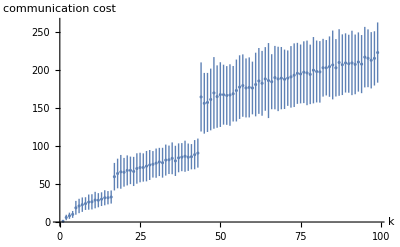

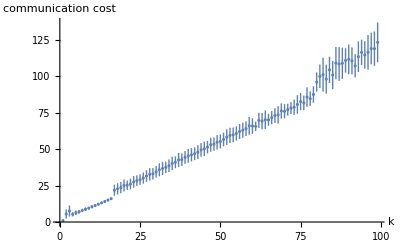

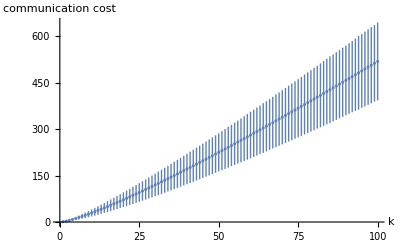

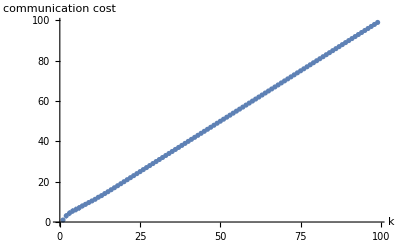

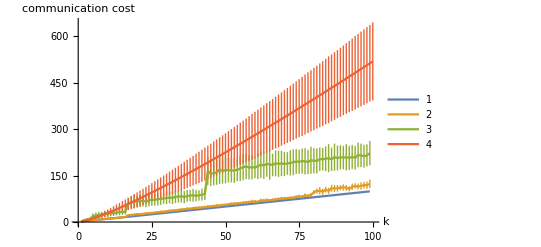

```mathematica
ListPlot[readyforplot[logm,logstd],AxesLabel->{k,"communication cost"}]
ListPlot[readyforplot[log2m,log2std],AxesLabel->{k,"communication cost"}]
ListPlot[readyforplot[ccm,ccstd],AxesLabel->{k,"communication cost"}]
ListPlot[readyforplot[lsm,lsstd],AxesLabel->{k,"communication cost"}]
ListPlot[{Legended[readyforplot[lsm,lsstd],"1"],Legended[readyforplot[log2m,log2std],"2"],Legended[readyforplot[logm,logstd],"3"],Legended[readyforplot[ccm,ccstd],"4"]},Joined->True,AxesLabel->{k,"communication cost"}]
```

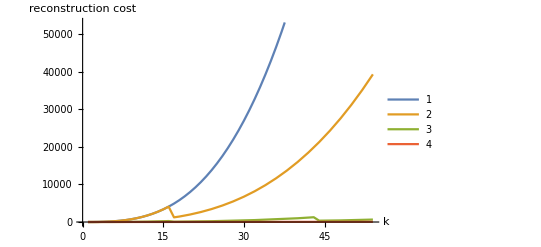

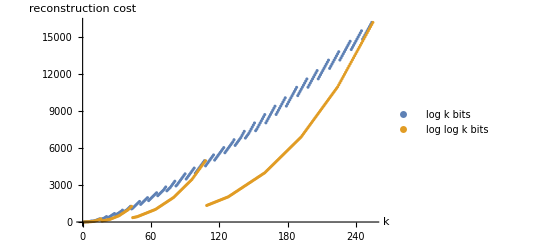

```mathematica
ListPlot[{Legended[lsrec[[1;;54]],"1"],Legended[log2rec[[1;;54]],"2"],Legended[logrec[[1;;54]],"3"],Legended[ccrec[[1;;54]],"4"]},Joined->True,AxesLabel->{k,"reconstruction cost"}]
ListPlot[{Legended[logreccont,"log k bits"],Legended[logrec,"log log k bits"]},AxesLabel->{k,"reconstruction cost"}]
```

```mathematica
logm/Range[Length[logm]]
```

{1,2.98,2.73733,2.498,3.7368,3.512,3.25657,3.027,2.90533,2.6508,2.62073,2.38633,2.30862,2.27571,2.12747,2.0525,3.504,3.542,3.46968,3.267,3.22876,3.08473,2.88835,2.92967,2.864,2.75554,2.71778,2.67571,2.61476,2.5776,2.54555,2.4345,2.46606,2.404,2.39086,2.23144,2.27935,2.24316,2.2159,2.1288,2.09278,2.10648,2.10586,3.73455,3.46684,3.41496,3.42562,3.53383,3.36367,3.34808,3.28078,3.19746,3.14785,3.12119,3.1416,3.16514,3.14505,3.03759,2.99749,2.93507,2.96138,2.98994,2.89295,2.93744,2.85926,2.79297,2.83182,2.76465,2.73965,2.67891,2.66231,2.64867,2.64247,2.63962,2.59376,2.58979,2.54442,2.48687,2.52491,2.47245,2.4356,2.47215,2.44227,2.43081,2.42762,2.35628,2.40906,2.34873,2.34858,2.31089,2.29684,2.25113,2.26052,2.20723,2.28017,2.24096,2.19085,2.1938,2.24909}

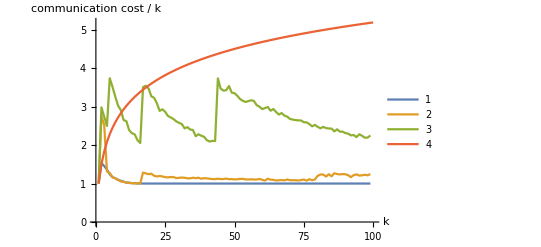

```mathematica
ListPlot[{Legended[lsm/Range[Length[lsm]],"1"],Legended[log2m/Range[Length[log2m]],"2"],Legended[logm/Range[Length[logm]],"3"],Legended[ccm/Range[Length[ccm]],"4"]},AxesLabel->{k,"communication cost / k"},Joined->True]
```